# Data preprocessing for complex Wilson network

## 1410.2546

### T = 210

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=210;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

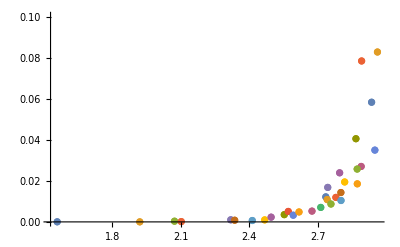

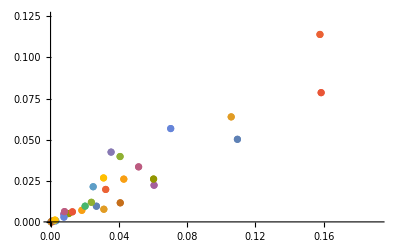

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

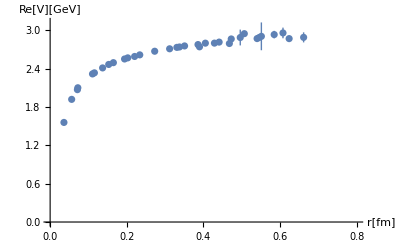

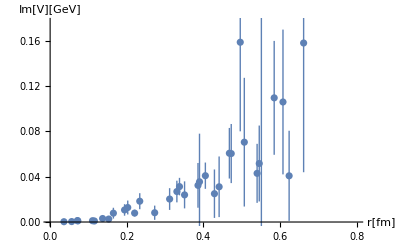

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

Note that in these paper data files the temperature is in Mev not GeV so we use 0.001T to plot in GeV

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T
```

0.21

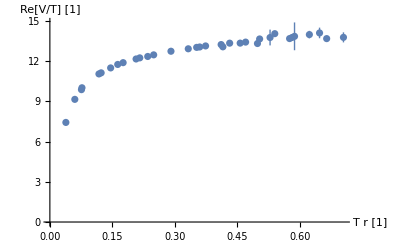

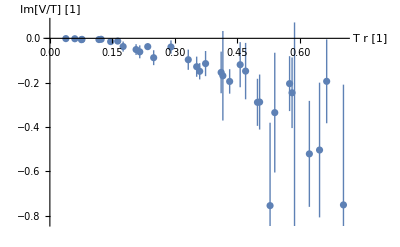

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT210.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT210.txt

### T = 252

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=252;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

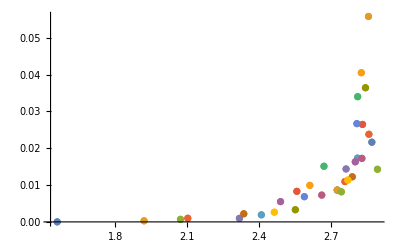

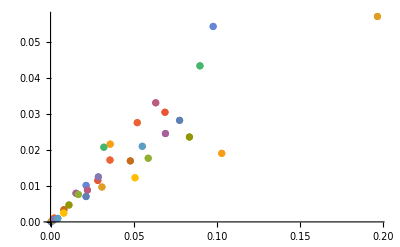

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

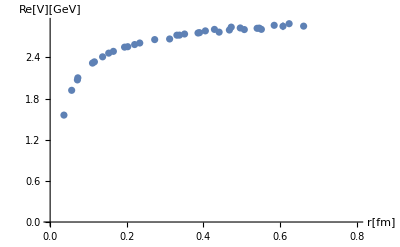

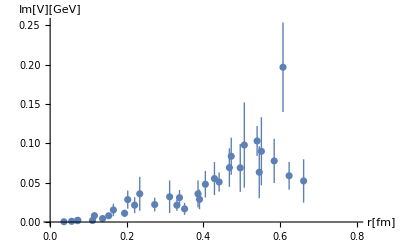

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T
```

0.252

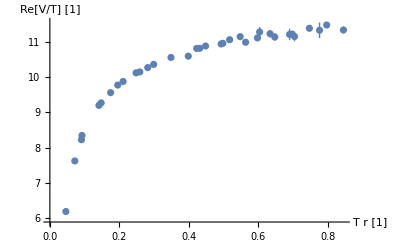

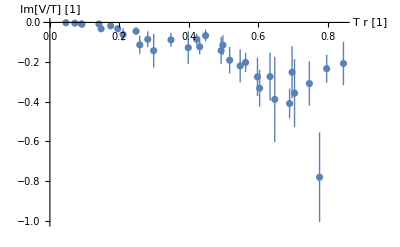

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT252.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT252.txt

### T = 280

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=280;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

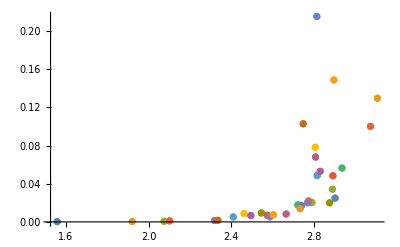

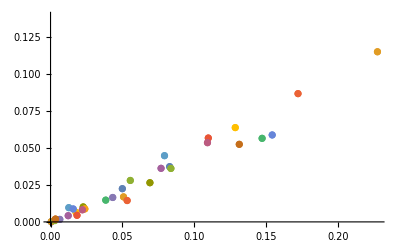

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

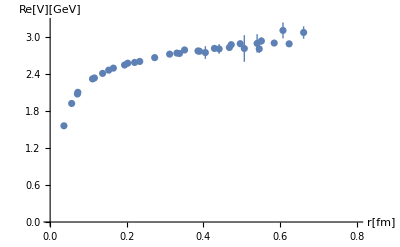

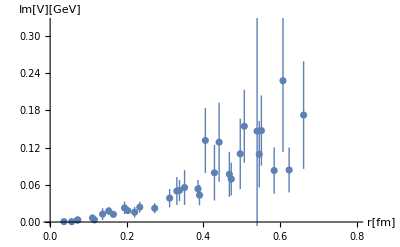

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T
```

0.28

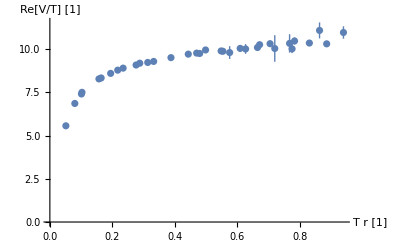

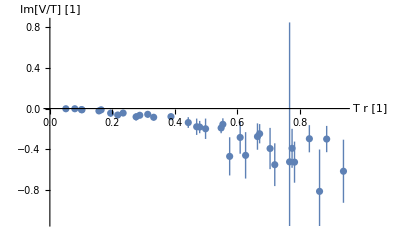

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT280.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT280.txt

### T = 315

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=315;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

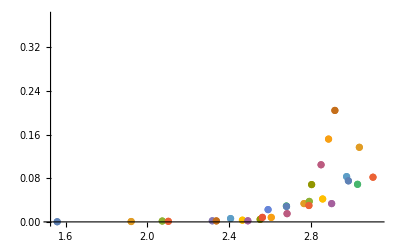

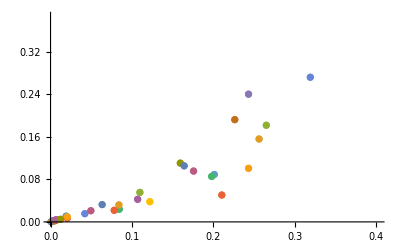

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

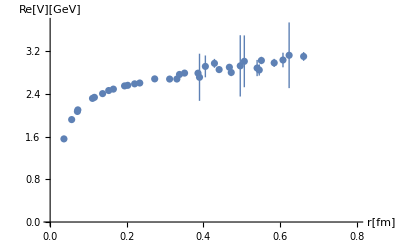

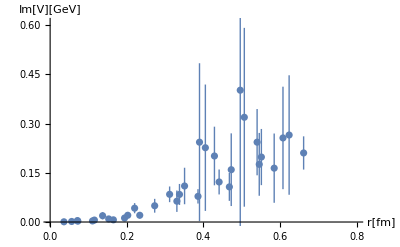

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T
```

0.315

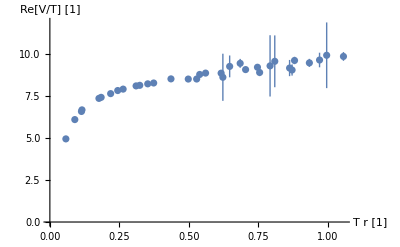

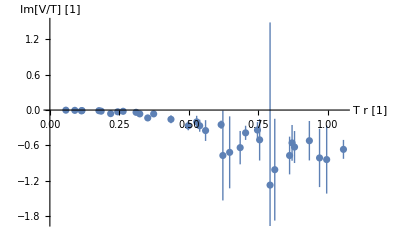

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT315.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT315.txt

### T = 360

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=360;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

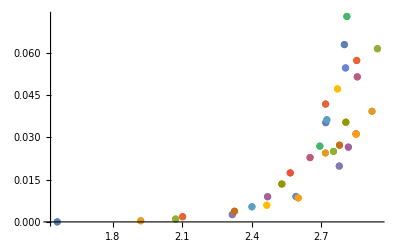

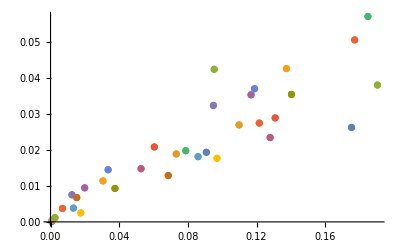

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

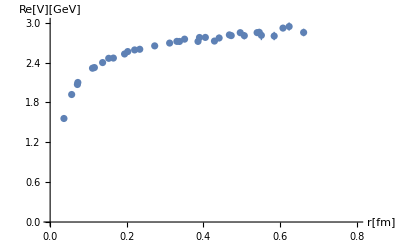

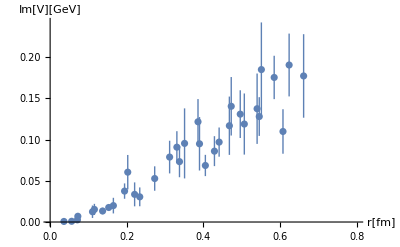

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T
```

0.36

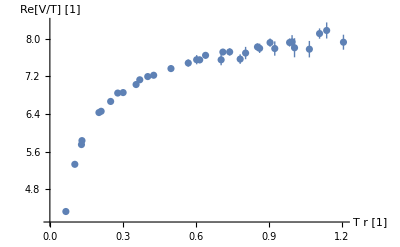

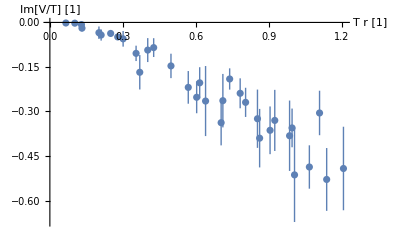

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT360.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT360.txt

### T = 420

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=420;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

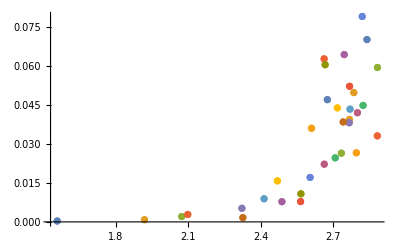

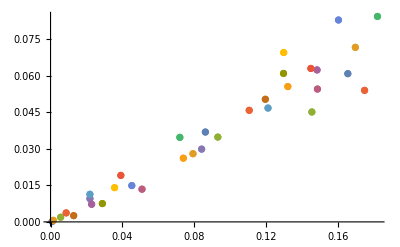

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

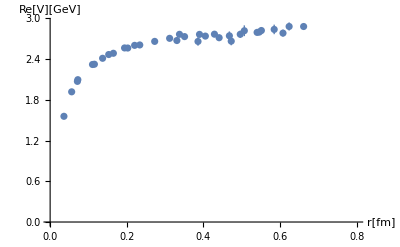

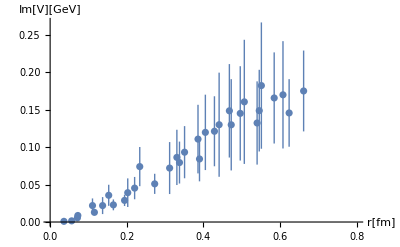

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T
```

0.42

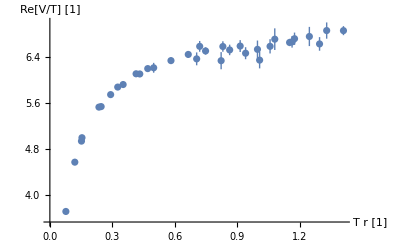

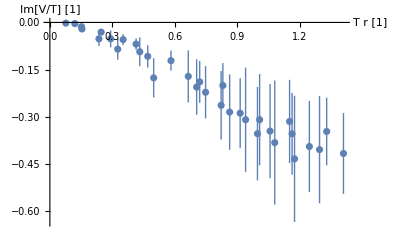

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT420.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT420.txt

### T = 503

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=503;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

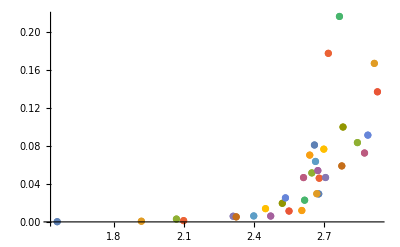

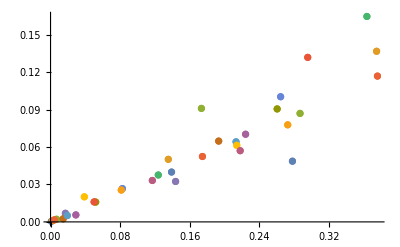

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

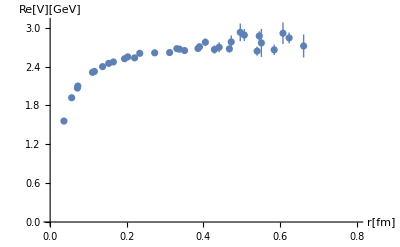

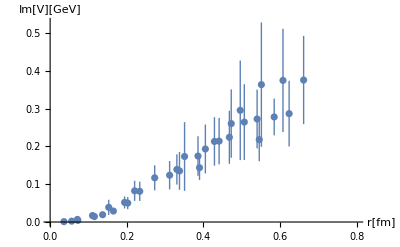

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T;
```

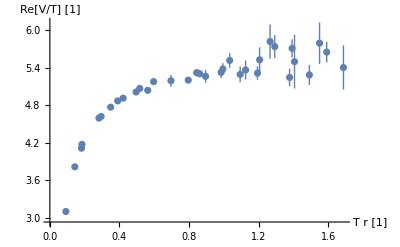

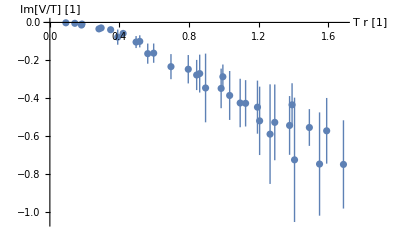

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT503.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT503.txt

### T = 629

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=629;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

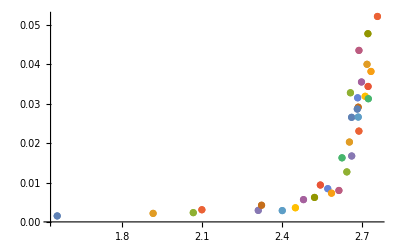

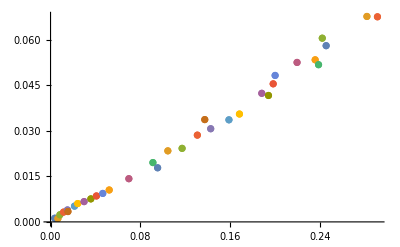

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

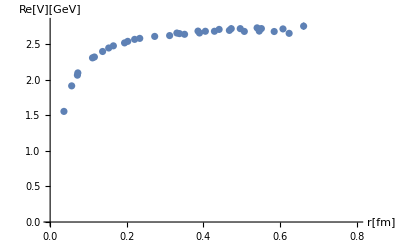

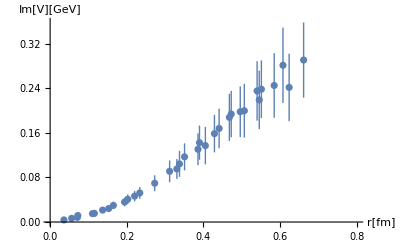

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T;
```

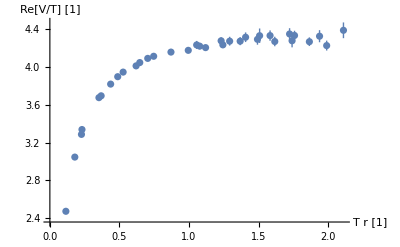

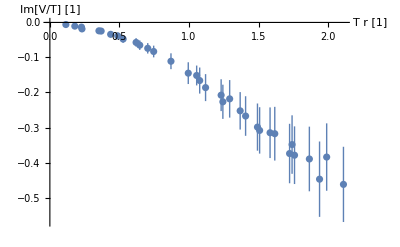

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT629.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT629.txt

### T = 839

Data columns are: “r [fm]” “ReV/ImV [GeV]” “Err[ReV] [GeV]”

```mathematica
T=839;
dataRe=Import[NotebookDirectory[]<>"data/1410.2546/ReV-Quenched/ReVT"<>ToString[T]<>".dat"];
dataIm=Import[NotebookDirectory[]<>"data/1410.2546/ImV-Quenched/ImVT"<>ToString[T]<>".dat"];
```

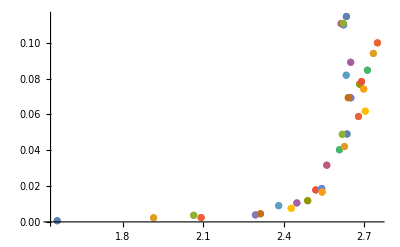

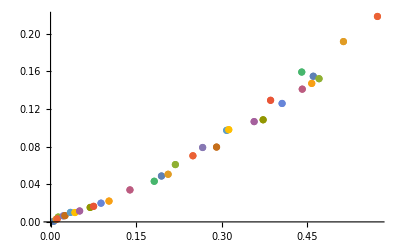

```mathematica
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

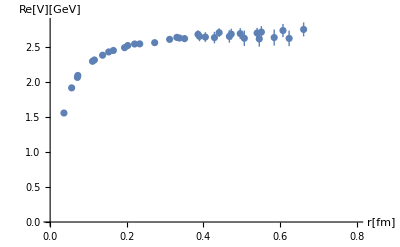

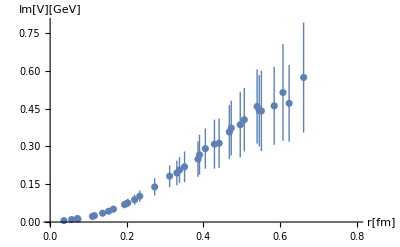

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,0.8},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
T=0.001T;
```

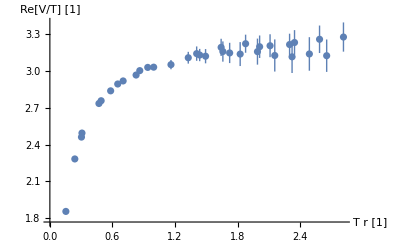

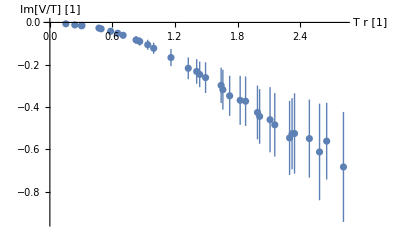

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"latticeT839.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/latticeT839.txt

## 1607.04049

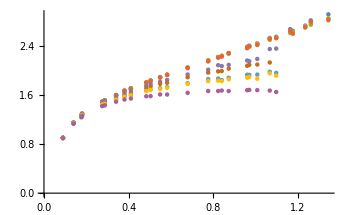

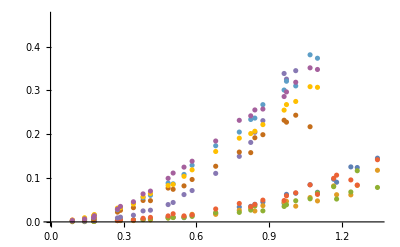

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataRe,First]//ListPlot
Thread[{#⟦;;,2⟧,#⟦;;,3⟧}]&/@GatherBy[dataIm,First]//ListPlot
```

### T = 113

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=1;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
(*T=0.312;*)
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.112778 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

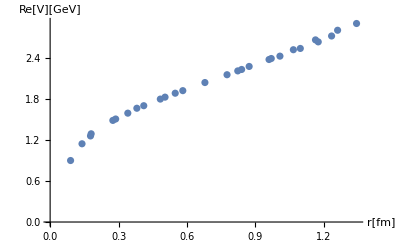

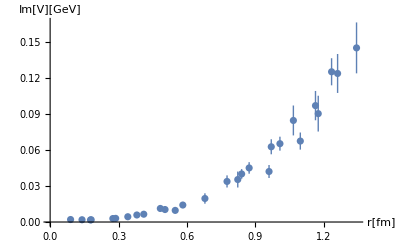

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

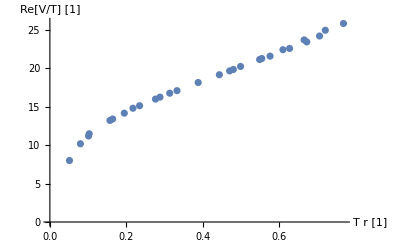

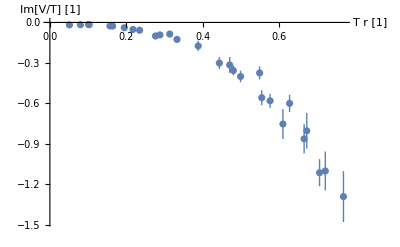

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT113.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT113.txt

### T = 226

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=2;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.225556 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

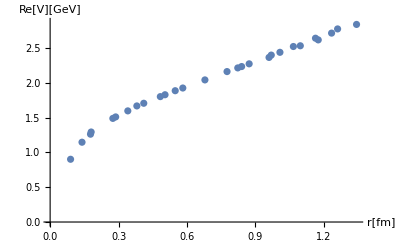

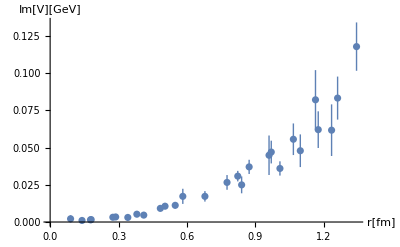

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

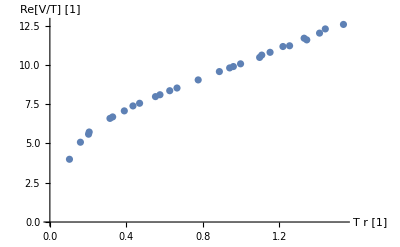

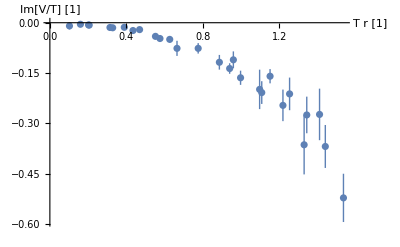

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT226.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT226.txt

### T = 254

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=3;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.25375 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

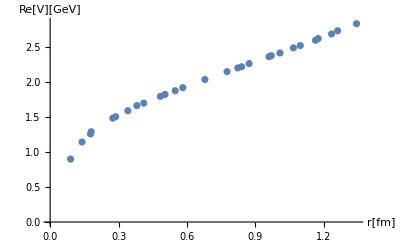

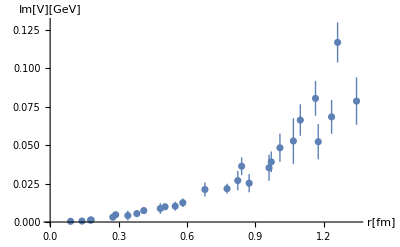

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

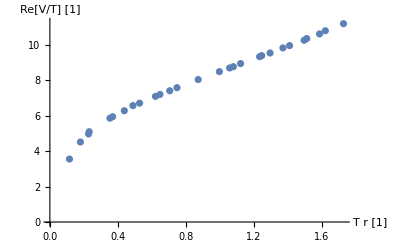

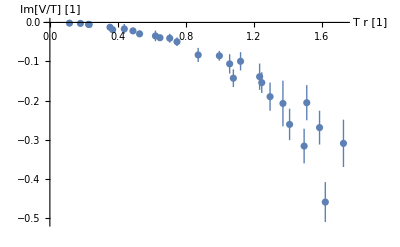

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT254.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT254.txt

### T = 271

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=4;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.270667 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

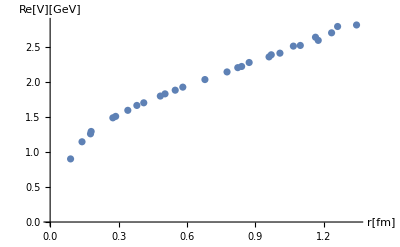

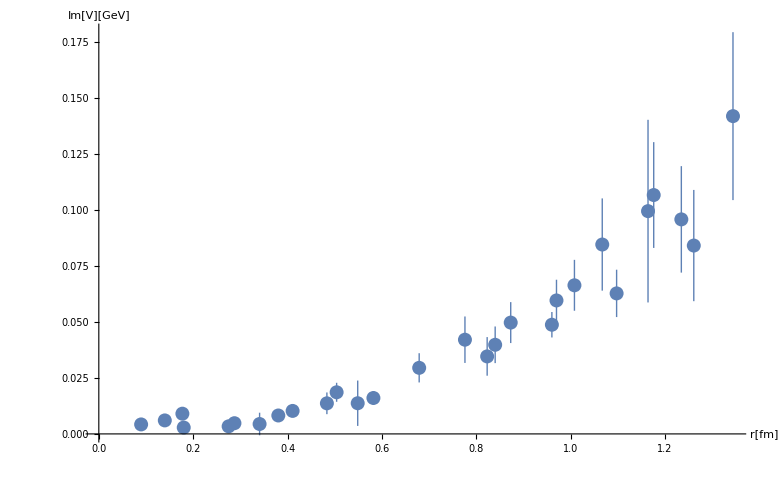

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

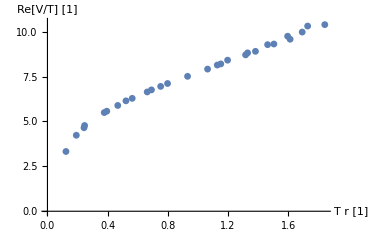

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

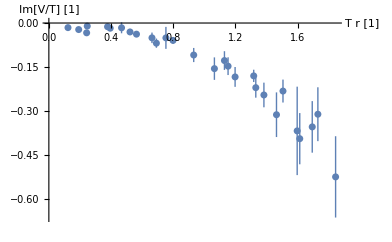

```mathematica
Export[]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT271.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT271.txt

### T = 290

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=5;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.29 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

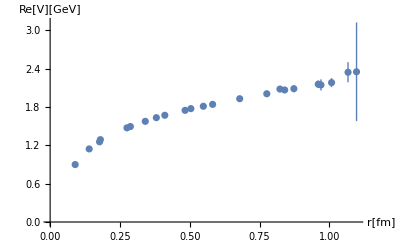

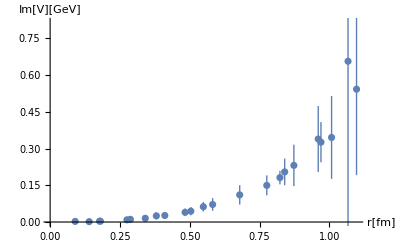

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

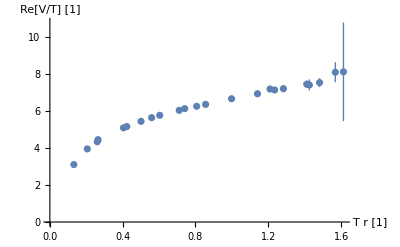

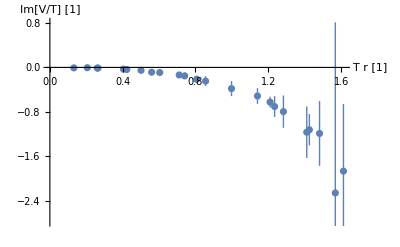

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT290.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT290.txt

### T = 312

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=6;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.312308 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

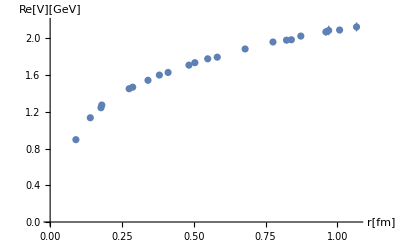

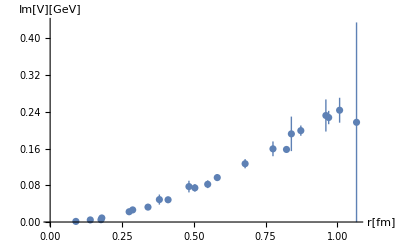

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

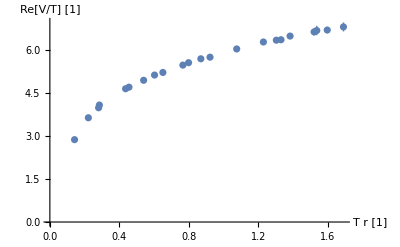

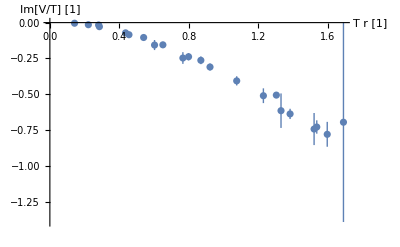

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT312.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT312.txt

### T = 338

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=7;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.338333 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

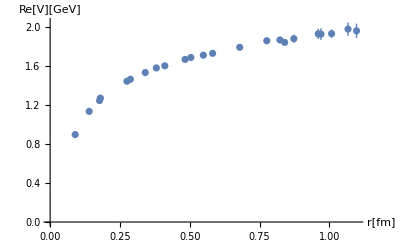

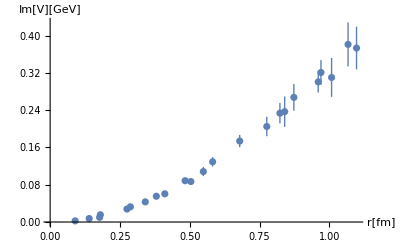

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

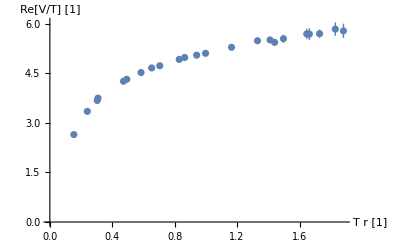

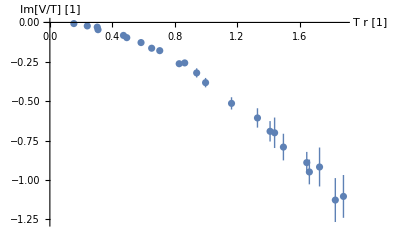

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT338.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT338.txt

### T = 369

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=8;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.369091 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

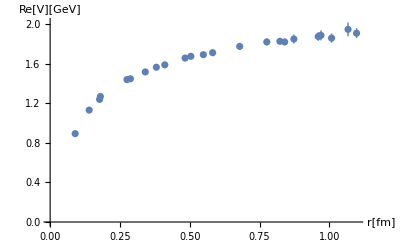

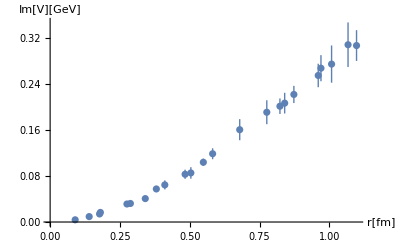

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

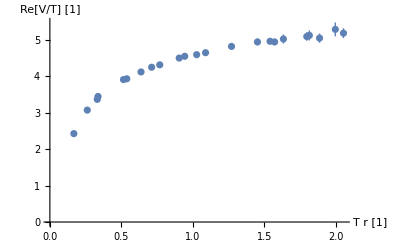

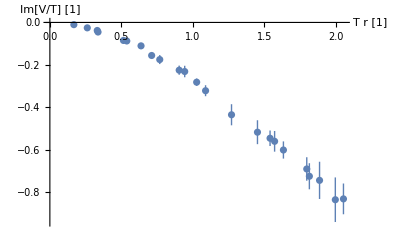

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT369.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT369.txt

### T = 406

```mathematica
dataRe=Import[NotebookDirectory[]<>"data/1607.04049/ReVQuenched.dat"];
dataIm=Import[NotebookDirectory[]<>"data/1607.04049/ImVQuenched.dat"];
Tidx=9;
Print["Using T = ",T=Union[dataRe⟦;;,1⟧]⟦Tidx⟧," GeV."]
dataRe=Rest/@Select[dataRe,First[#]==T&];
dataIm=Rest/@Select[dataIm,First[#]==T&];
```

Using T = 0.406 GeV.

```mathematica
l=dataRe⟦;;,1⟧;
l==dataIm⟦;;,1⟧
ReV=dataRe⟦;;,2⟧;
ReVσ=dataRe⟦;;,3⟧;
ImV=dataIm⟦;;,2⟧;
ImVσ=dataIm⟦;;,3⟧;
```

True

This plot doesn’t have the manual shifts that Fig. 2 has.

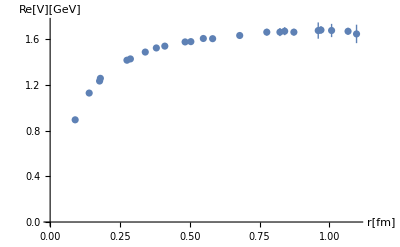

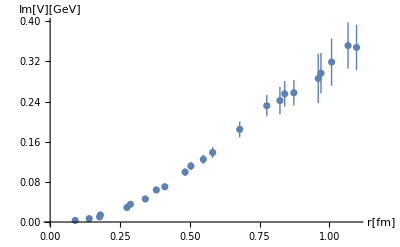

```mathematica
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataRe,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Re[V][GeV]"}]
ListPlot[{#⟦1⟧,Around[#⟦2⟧,#⟦3⟧]}&/@dataIm,PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"r[fm]","Im[V][GeV]"}]
```

Interestingly, the dataset seems to be missing a few data points compared to Fig. 2. Im[V] extends to slightly higher r in the paper.

### Export data

Our statistical model expects data in the dimensionless combinations (T r,V/T). In addition, we assume that Im[V] in the data files is actually |Im[V]| and we flip the sign of Im[V] to negative.

```mathematica
fmToInvGeV[fm_]:=5.068fm
```

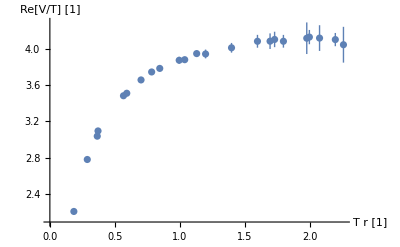

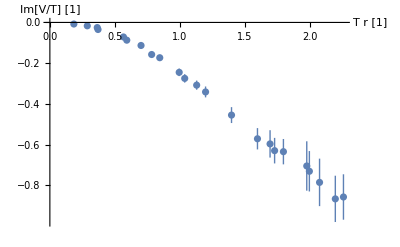

```mathematica
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataRe,AxesLabel->{"T r [1]","Re[V/T] [1]"}]
ListPlot[{T fmToInvGeV[#⟦1⟧],Around[-(#⟦2⟧)/T,(#⟦3⟧)/T]}&/@dataIm,AxesLabel->{"T r [1]","Im[V/T] [1]"}]
```

```mathematica
Export[NotebookDirectory[]<>"1607latticeT406.txt",{T fmToInvGeV[l],ReV/T,ReVσ/T,-ImV/T,ImVσ/T},"Table"]
```

/home/local/htakko/Dropbox/Own/deep-learning-EE/env/complex_wilson/1607latticeT406.txt